#### SOLITON SG - equation

```mathematica
v1=-0.5;
v2=0.5;
x10=-10;
x20=10;
fun[x_,x0_,v_]:=4*ArcTan[Exp[(x-x0)/Sqrt[1-v^2]]];
(*f10=4*ArcTan[Exp[(x-x10-v1*t)/Sqrt[1-v1^2]]];
f20=4*ArcTan[Exp[(x-x20-v2*t)/Sqrt[1-v2^2]]];
ff=(f10+f20)/.t->0;
df10=ReplaceAll[D[f10,t],t->0];
df20=ReplaceAll[D[f20,t],t->0];*)
xmin=-40;
xmax=40;
dx = 0.01;
tmax=105;
f1=Interpolation[Map[{#,fun[#,x10,v1]}&,Range[xmin,xmax,dx]],InterpolationOrder->2];
f2=Interpolation[Map[{#,fun[#,x20,v2]}&,Range[xmin,xmax,dx]],InterpolationOrder->2];
df1=f1';
df2=f2';
```

```mathematica
solution=f/.First[NDSolve[{D[f[t,x], {t},{t}]-D[f[t,x], {x},{x}]+Sin[f[t,x]]==0,f[0,x]==f1[x]+f2[x],Derivative[1,0][f][0,x]==v1*df1[x]+v2*df2[x],f[t,xmin]==f1[xmin]+f2[xmin],f[t,xmax]==f1[xmax]+f2[xmax]},f,{t,0,tmax},{x,xmin,xmax}]];
```

```mathematica
Manipulate[
Plot[Derivative[1,0][solution][t,x],{x,xmin,xmax},PlotRange->All],
{t,0,tmax,0.1}]
```

```mathematica
v=0.5;
x0=0;
fun[x_,x0_,v_]:=4*ArcTan[Exp[(x-x0)/Sqrt[1-v^2]]];
xmin=-40;
xmax=40;
dx = 0.01;
tmax=15;
f0=Interpolation[Map[{#,fun[#,x0,v]}&,Range[xmin,xmax,dx]],InterpolationOrder->2];
df0=f0';
```

```mathematica
solution=f/.First[NDSolve[{D[f[t,x], {t},{t}]-D[f[t,x], {x},{x}]+Sin[f[t,x]]==0,f[0,x]==f0[x],Derivative[1,0][f][0,x]==v*df0[x],f[t,xmin]==f0[xmin],f[t,xmax]==f0[xmax]},f,{t,0,tmax},{x,xmin,xmax}]];
```

#### KINK KK - equation

```mathematica
b=1;
x0=5;
xmin=-15.0;
xmax=15.0;
tmin=0.0;
tmax=20.0;
count=0;
v=0.5;
F[b_,alpha_]:=NIntegrate[1/Sqrt[Sqrt[1+b^2*(1-Cos[x])]-1],{x,Pi,alpha},MaxRecursion->1000]
```

```mathematica
list=ParallelTable[{F[b,alpha]/2,alpha},{alpha,10^-6,2*Pi,0.00001}];//AbsoluteTiming
```

$Aborted

```mathematica
fun=Interpolation[list,InterpolationOrder->2];
maxKsi=Max[list[[All,1]]];
minKsi=Min[list[[All,1]]];
kink[x_]:=Piecewise[{{fun[x],x≤ maxKsi&&x≥ minKsi},{N[2*Pi],x≥maxKsi},{0.0,x≤minKsi}}];
```

```mathematica
DumpSave[NotebookDirectory[]<>"/list.mx",list];
```

```mathematica
str=OpenRead[NotebookDirectory[]<>"/list-b15-v5.mx"];
Get[str];
Close[str];
```

```mathematica
sol={};
listk=Table[{x,kink[x]},{x,2*xmin,2*xmax,0.00001}];
k=Interpolation[listk,InterpolationOrder->2];
dk=k';
Clear[f];
Print["Step #"<>ToString[1]];
alpha=10;
nn0=10;
solution=f/.First[NDSolve[{D[f[t,x], t,t]==D[f[t,x], x,x]-(1+nn0*alpha/Sqrt[Pi]*Exp[-(alpha*x)^2])*b^2*Sin[f[t,x]]/Sqrt[1+b^2*(1-Cos[f[t,x]])],f[0,x]==k[(x-x0)/Sqrt[1-v^2]],Derivative[1,0][f][0,x]==v*k'[(x-x0)/Sqrt[1-v^2]]/Sqrt[1-v^2],f[t,xmin]==0,f[t,xmax]==2*Pi},f,{t,0,tmax},{x,xmin,xmax}, MaxSteps->{10000,100000}]];
AppendTo[sol,Table[{x,Derivative[0,1][solution][0,x]},{x,xmin,xmax, 0.001}]];
AppendTo[sol,Table[{x,Derivative[0,1][solution][tmax,x]},{x,xmin,xmax, 0.001}]];
Do[
Print["Step #"<>ToString[i+1]];
listk=Table[{x,solution[tmax,x]},{x,xmin,xmax,0.00001}];
k=Interpolation[listk,InterpolationOrder->2];
dk=k';
Clear[f];
solution=f/.First[NDSolve[{D[f[t,x], t,t]==D[f[t,x], x,x]-b^2*Sin[f[t,x]]/Sqrt[1+b^2*(1-Cos[f[t,x]])],f[0,x]==k[x],Derivative[1,0][f][0,x]==v*k'[x],f[t,xmin]==0,f[t,xmax]==2*Pi},f,{t,0,tmax},{x,xmin,xmax}, MaxSteps->{10000,100000}]];
AppendTo[sol,Table[{x,Derivative[0,1][solution][tmax,x]},{x,xmin,xmax, 0.001}]];
,{i,count}];
 Print["Done"];
```

Step #1

NDSolve::mxsst: Using maximum number of grid points 100000 allowed by the MaxPoints or MinStepSize options for independent variable x.

Done

```mathematica
mas=Table[{{x,Derivative[0,1][solution][0,x]},{x,Derivative[0,1][solution][tmax,x]}},{x,xmin,xmax, 0.01}];
```

```mathematica
p1=ListLinePlot[mas[[All,1]],PlotRange->{{3,7},{-0.001,0.1}},InterpolationOrder->1,AxesStyle->Directive[12],PlotStyle->Red,GridLines->Automatic,AxesOrigin->{7,0}];
p2=ListLinePlot[mas[[All,2]],PlotRange->{{-7,-3},{-0.001,0.1}},InterpolationOrder->1,AxesStyle->Directive[12],GridLines->Automatic,AxesOrigin->{-7,0}];
```

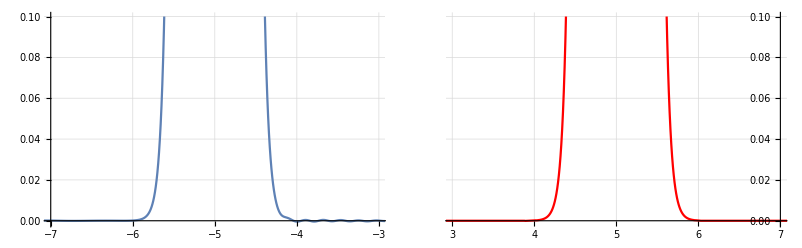

```mathematica
GraphicsRow[{p2,p1},Frame->False,Spacings->{0,0}]
```

```mathematica
Export[NotebookDirectory[]<>"sol1-b15-v5-t0.dat",mas[[All,1]],"CSV"]
Export[NotebookDirectory[]<>"sol1-b15-v5-tmax.dat",mas[[All,1]],"CSV"]
```

C:\Users\user\YandexDisk\CurrentWorks\2018_KKeq\sol1-b15-v5-t0.dat

C:\Users\user\YandexDisk\CurrentWorks\2018_KKeq\sol1-b15-v5-tmax.dat

#### SMALL AMPLITUDE BION KK - equation

#### ϵ^3 - approximation

```mathematica
b=10;
x0=0;
xmin=-200.0;
xmax=200.0;
tmin=0.0;
tmax=200.0;
w=0.1;
eps=Sqrt[1-w^2];
beta=(1/6+b^2/4);
gamma=1/480*(-4-30*b^2-45*b^4);
f0 = (Sqrt[8/(3*beta)]*eps*((1/36)*eps^2*(2 - 1/Cosh[eps*x]^2) + 1)*Cos[t*w])/Cosh[eps*x] - (eps^2*(eps^2/6 + 11/(2*Cosh[eps*x]^2) + 1)*Cos[3*t*w])/
     Cosh[eps*x]^2/12;
df0t=D[f0,t];
df0x=D[f0,x];
```

```mathematica
Clear[f];
solution=f/.First[NDSolve[{D[f[t,x], t,t]==D[f[t,x], x,x]-Sin[f[t,x]]/Sqrt[1+b^2*(1-Cos[f[t,x]])],f[0,x]==f0/.(t->0),Derivative[1,0][f][0,x]==df0t/.(t->0),f[t,xmin]==f0/.(x->xmin),f[t,xmax]==f0/.(x->xmax)},f,{t,0,tmax},{x,xmin,xmax}]]
```

InterpolatingFunction[{{0., 200.}, {-200., 200.}}, <>]

```mathematica
Manipulate[
Plot[Derivative[1,0][solution][t,x],{x,xmin,xmax},PlotRange->All],
{t,0,tmax,0.1}]
```

InterpolatingFunction::dmval: Input value {127.1,-49.998} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {127.1,-29.9988} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {127.1,-49.998} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {127.1,-34.9986} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
Series[-beta^2*Sin[u]/Sqrt[1+beta^2*(1-Cos[u])],{u,0,5}]
```

-beta^2 u+(beta^2/6+beta^4/4) u^3+1/480 (-4 beta^2-30 beta^4-45 beta^6) u^5+O[u]^6

#### KINK-ANTIKINK COLLISION IN KK - equation

```mathematica
b=15;
x10=5;
x20=-5;
xmin=-10.0;
xmax=10.0;
tmin=0.0;
tmax=20.0;
v1=0.5;
v2=-0.5;
F[b_,alpha_]:=NIntegrate[1/Sqrt[Sqrt[1+b^2*(1-Cos[x])]-1],{x,Pi,alpha},MaxRecursion->1000]
```

```mathematica
list=ParallelTable[{F[b,alpha]/2,alpha},{alpha,10^-6,2*Pi,0.00001}];//AbsoluteTiming
```

{380.327,Null}

```mathematica
str=OpenRead[NotebookDirectory[]<>"/list.mx"];
Get[str];
Close[str];
```

```mathematica
fun=Interpolation[list,InterpolationOrder->2];
maxKsi=Max[list[[All,1]]];
minKsi=Min[list[[All,1]]];
kink[x_]:=Piecewise[{{fun[x],x≤ maxKsi&&x≥ minKsi},{N[2*Pi],x≥maxKsi},{0.0,x≤minKsi}}];
```

```mathematica
listk=Table[{x,kink[x]},{x,2*xmin,2*xmax,0.00001}];
k=Interpolation[listk,InterpolationOrder->2];
dk=k';
```

```mathematica
f0=k[(x-x10)/Sqrt[1-v1^2]]+k[(x-x20)/Sqrt[1-v2^2]];
fd0=v1*k'[(x-x10)/Sqrt[1-v1^2]]/Sqrt[1-v1^2]+v2*k'[(x-x20)/Sqrt[1-v2^2]]/Sqrt[1-v2^2];
Clear[f];
solution=f/.First[NDSolve[{D[f[t,x], t,t]==D[f[t,x], x,x]-b^2*Sin[f[t,x]]/Sqrt[1+b^2*(1-Cos[f[t,x]])],
f[0,x]==f0,Derivative[1,0][f][0,x]==fd0,f[t,xmin]==0,f[t,xmax]==4*Pi},
f,{t,0,tmax},{x,xmin,xmax}, MaxSteps->{10000,100000}]];
```

NDSolve::mxsst: Using maximum number of grid points 100000 allowed by the MaxPoints or MinStepSize options for independent variable x.

NDSolve::mxst: Maximum number of 10000 steps reached at the point t == 5.00999.

NDSolve::eerr: Warning: scaled local spatial error estimate of 1329.02 at t = 5.00999 in the direction of independent variable x is much greater than the prescribed error tolerance. Grid spacing with 100001 points may be too large to achieve the desired accuracy or precision. A singularity may have formed or a smaller grid spacing can be specified using the MaxStepSize or MinPoints method options.

```mathematica
mas=Table[{{x,Derivative[0,1][solution][0,x]},{x,Derivative[0,1][solution][tmax,x]}},{x,-10,10, 0.05}];
```

```mathematica
p1=ListLinePlot[mas[[All,1]],PlotRange->{{-6,-4},{-0.1,0.5}},InterpolationOrder->1,AxesStyle->Directive[12],PlotStyle->Red,GridLines->Automatic,AxesOrigin->{-4,0}];
p2=ListLinePlot[mas[[All,2]],PlotRange->{{4,6.5},{-0.1,0.5}},InterpolationOrder->1,AxesStyle->Directive[12],GridLines->Automatic,AxesOrigin->{4,0}];
```

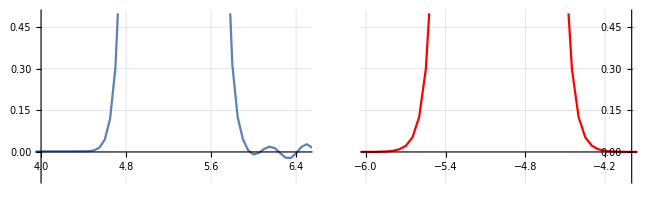

```mathematica
GraphicsRow[{p2,p1},Frame->False,Spacings->{0,0}]
```

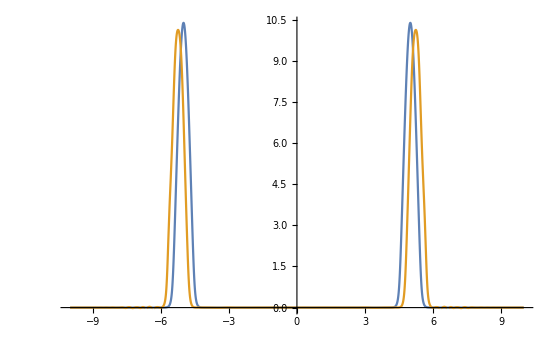

```mathematica
plt=Plot[{Derivative[0,1][solution][0,x],Derivative[0,1][solution][tmax,x]},{x,xmin,xmax},PlotRange->{-0.02,All}]
```

#### CORRELATE ANALYSIS

```mathematica
GetKinkCenters[efun_,time_,xmin_,xmax_]:=Module[{nx=1000,emas,emax},
emas=Array[efun[time,#]&, nx, {xmin,xmax}];
emax=TakeLargest[emas,1][[1]];
Return[{emas,Position[emas,emax][[1]][[1]]}];
];
GetCorrelate[efun_,time1_,time2_,xmin1_,xmax1_,xmin2_,xmax2_]:=Module[{emas1,emas2,pos1,pos2,lencorr=100, emas1corr,emas2corr},
{emas1,pos1}=GetKinkCenters[efun,time1,xmin1,xmax1];
{emas2,pos2}=GetKinkCenters[efun,time2,xmin2,xmax2];
emas1corr=emas1[[pos1-lencorr;;pos1+lencorr]];
emas2corr=emas2[[pos2-lencorr;;pos2+lencorr]];
Correlation[emas1corr,emas2corr]
]
```

```mathematica
GetCorrelate[Derivative[0,1][solution],0,tmax,-4,-3,3,7]
```

$Aborted

```mathematica
tau=5;
GetCorrelate[Derivative[0,1][solution],0,tau,x0-2,x0+2,x0-v*tau-2,x0-v*tau+2]
```

0.997019

```mathematica
cor=Map[{#,GetCorrelate[Derivative[0,1][solution],0,#,x0-2,x0+2,x0-v*#-2,x0-v*#+2]}&,Array[#&,10,{0,tmax}]]
```

{{0.,1.},{2.22222,0.9994},{4.44444,0.999999},{6.66667,0.999996},{8.88889,0.999989},{11.1111,0.999974},{13.3333,0.999947},{15.5556,0.999901},{17.7778,0.999832},{20.,0.999732}}

```mathematica
Export[NotebookDirectory[]<>"cor.dat",cor]
```

C:\Users\user\YandexDisk\CurrentWorks\2018_KKeq\cor.dat

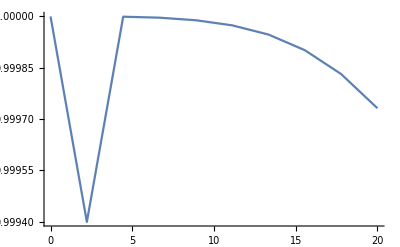

```mathematica
ListLinePlot[cor]
```

#### KINK KK - equation with HF field

```mathematica
a=1;
b=1;
x0=5;
xmin=-15.0;
xmax=15.0;
tmin=0.0;
tmax=2.0;
count=0;
v=0.5;
```

```mathematica
F0[alpha_]:=NIntegrate[Sqrt[1+b^2*(1-Cos[alpha + a*Sin[t]])],{t,0,2*Pi}]/Pi;
R0[alpha_]:=Quiet[NIntegrate[b^2*Sin[alpha + a*Sin[t]]/Sqrt[1+b^2*(1-Cos[alpha + a*Sin[t]])],{t,0,2*Pi}]/2/Pi];
F0List=ParallelMap[{#,F0[#]}&,Subdivide[0,2*Pi,1000]];
R0List=ParallelMap[{#,R0[#]}&,Subdivide[0,2*Pi,1000]];
R0Interp=Interpolation[R0List,InterpolationOrder->2];
F0Interp=Interpolation[F0List,InterpolationOrder->2];
F[alpha_]:=NIntegrate[1/Sqrt[F0Interp[alpha]-F0Interp[0]],{t,0,2*Pi},{x,Pi,alpha},MaxRecursion->1000]
```

```mathematica
list=ParallelTable[{F[alpha]/Sqrt[2],alpha},{alpha,10^-6,2*Pi,0.001}];//AbsoluteTiming
```

{9.2591,Null}

```mathematica
fun=Interpolation[list,InterpolationOrder->2];
maxKsi=Max[list[[All,1]]];
minKsi=Min[list[[All,1]]];
kink[x_]:=Piecewise[{{fun[x],x≤ maxKsi&&x≥ minKsi},{N[2*Pi],x≥maxKsi},{0.0,x≤minKsi}}];
```

```mathematica
DumpSave[NotebookDirectory[]<>"/list.mx",list];
```

```mathematica
str=OpenRead[NotebookDirectory[]<>"/list-b15-v5.mx"];
Get[str];
Close[str];
```

```mathematica
sol={};
listk=Table[{x,kink[x]},{x,2*xmin,2*xmax,0.001}];
k=Interpolation[listk,InterpolationOrder->2];
dk=k';
Clear[f];
solution=f/.First[NDSolve[{D[f[t,x], t,t]==D[f[t,x], x,x]-R0Interp[f[t,x]],f[0,x]==k[(x-x0)/Sqrt[1-v^2]],Derivative[1,0][f][0,x]==v*k'[(x-x0)/Sqrt[1-v^2]]/Sqrt[1-v^2],f[t,xmin]==0,f[t,xmax]==2*Pi},f,{t,0,tmax},{x,xmin,xmax}, MaxSteps->{10000,100000}]];
 Print["Done"];
```

Done

```mathematica
mas=Table[{{x,Derivative[0,1][solution][0,x]},{x,Derivative[0,1][solution][tmax,x]}},{x,xmin,xmax, 0.01}];
```

```mathematica
p1=ListLinePlot[mas[[All,1]],PlotRange->{{3,7},{-0.001,0.1}},InterpolationOrder->1,AxesStyle->Directive[12],PlotStyle->Red,GridLines->Automatic,AxesOrigin->{7,0}];
p2=ListLinePlot[mas[[All,2]],PlotRange->{{-7,-3},{-0.001,0.1}},InterpolationOrder->1,AxesStyle->Directive[12],GridLines->Automatic,AxesOrigin->{-7,0}];
```

```mathematica
GraphicsRow[{p2,p1},Frame->False,Spacings->{0,0}]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"sol1-b15-v5-t0.dat",mas[[All,1]],"CSV"]
Export[NotebookDirectory[]<>"sol1-b15-v5-tmax.dat",mas[[All,1]],"CSV"]
```

C:\Users\user\YandexDisk\CurrentWorks\2018_KKeq\sol1-b15-v5-t0.dat

C:\Users\user\YandexDisk\CurrentWorks\2018_KKeq\sol1-b15-v5-tmax.dat